## Въведение

Wolfram Mathematica е интерактивна система за компютърна алгебра. Тя е базирана на езикът за програмиране Wolfram Language. С помощта на системата, разбира се, могат да се правят сравнително прости пресмятания - такива, каквито бихме могли да направим с обикновен калкулатор:

```mathematica
7+5 (*Оценяване на стойността на израз: Shift + Enter/Numeric Enter*)
```

12

```mathematica
3/5
7*12 
7 12
Sqrt[5]
√5
8/120
10^5
10^5
```

3/5

84

84

√5

√5

1/15

100000

100000

Една от ключовите функциoналности на системата Mathematica e, че може да работи със символни изрази. Нещо повече, по подразбиране тя смята символно, освен ако не е указано друго.

```mathematica
x+5y+x+y-x
```

x+6 y

```mathematica
Simplify[Sin[x]^2+Cos[x]^2]
```

1

```mathematica
Integrate[1/(1+x^4),x]
```

(-2 ArcTan[1-√2 x]+2 ArcTan[1+√2 x]-Log[1-√2 x+x^2]+Log[1+√2 x+x^2])/(4 √2)

### Приоритет на операциите

```mathematica
3*4+1
```

13

```mathematica
3*(4+1)
```

15

```mathematica
-3^2
```

-9

```mathematica
(-3)^2
```

9

## Вградени функции (команди)

Правила при въвеждане на команди:
	* Името на всяка вградена команда започва с главна буква. Ако името се състои от повече от една дума (напр. ArcSin), то всяка отделна дума започва с главна буква, без разстояние помежду им.
	* Аргументите на командите се поставят в единични квадратни скоби.
	* Ако дадена функция приема повече от един аргумент, всеки следващ се отделя със запетая от предходния.

```mathematica
Max[1,2,4,8,0]
```

8

```mathematica
Log[1]
```

0

```mathematica
Log(1) (*Червени скоби - некоректен синтаксис*)
```

Log

```mathematica
log[1] (*Името на функцията е оцветено в син цвят - не се разпознава командата*)
```

log[1]

```mathematica
Mod[20,3] (*Двуаргументна команда - дава остатъка при деление*)
```

2

```mathematica
(*Вградените тригонометрични функции приемат аргумент в радиани*)
Cos[π/4]
```

1/(√2)

```mathematica
Sin[2Pi]
```

0

```mathematica
Log[ⅇ]
```

1

```mathematica
Log[E]
```

1

```mathematica
D[x^2+5,x]
```

2 x

```mathematica
Integrate[1/(x^3+1),x]
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
Integrate[(1+x^3)/4,{x,1,5}]
```

40

Повечето вградени функции носят имена, които са същестуващи думи в англисйкия език, или техни съкращения. Когато искаме да отркием дали съществува дадена функция, вградена в езика, е удобно да използваме документацията, като е достатъчно просто да въведем реалното название на операцията, която искаме да изпълним (напр. Integrate, FindMaximum, FindRoot и т.н.)

### Оператори за сравнение и логически операции

```mathematica
4≥5
```

False

```mathematica
√785875≤ 45
```

False

```mathematica
(23<57)&&(π∈Integers)
```

False

```mathematica
(23<57)||(π∈Integers)
```

True

```mathematica
(23<57)&&!(π∈Integers)
```

```mathematica
True
```

### Структура на системата

Системата е разделена на две подпрограми - kerenel и front-end. Front end-ът е свързан с потребителския интерфейс - начинът,  посредством който потребителят комуникира със системата. 
Интерфейсът предоставя възможност за създаване и редактиране на файлове (Mathematica notebooks). Тези файлове са с разширение .nb. Ядрото (the kernel) интерпретира изрази от езика Wolfram и връща резултатни такива. Ядрото се зарежда автоматично при оценяване на първата въведена команда. Поради тази причина би могло да има значително забаявне по време на първото изчисление.
Както забелязваме, всеки notebook е разделен на отделни единици, наречени клетки (cells). Обхвата на дадена клетка се обозначава от квадратните скоби в дясната част на файла. Клетките са вложени една в друга йерархично и служат за структуриране на документа. 
Сливане на клетки --> Ctrl+Shift +M
Разделяне на клетки --> Ctrl+Shfift+D

```mathematica
500*100
50000
20*10
200
```

```mathematica
% (*Извиква последно изведения резултат*)
```

1000

```mathematica
%^2
```

1000000

## Символни и числени пресмятания

По подразбиране Matehmatica смята символно, следователно - точно. Това обаче невинаги възможно. Понякога може да доведе и до сериозни проблеми с изчисленията.

```mathematica
Sin[Pi/5]
```

√(5/8-(√5)/8)

```mathematica
Log[15]
```

Log[15]

```mathematica
Log[15.] (*По подразбиране, изведеният резултат се закръглява до 6 знака.*)
```

2.70805

```mathematica
N[Log[15]] (*Функцията N връща числена апроксимация на търсения резултат.*)
```

2.70805

```mathematica
Log[15]//N
```

2.70805

```mathematica
(√3)^2
```

3

```mathematica
(√3.)^2 (*Тъй като това е числена апроксимация, получаваме резултат с ограничена точност.*)
```

3.

```mathematica
2.9999999999999996
```

```mathematica
255^30
```

1571105731713312715511913444948824285516982702388429082930088043212890625

```mathematica
N[255^30] (*Scientific notation. Очевидно апроксимация, значещите цифри са ограничени до 6-тия знак.*)
```

1.57111×10^72

```mathematica
N[255^30,50] (*Указване на точност*)
```

1.5711057317133127155119134449488242855169827023884×10^72

```mathematica
(*1245878541254^(10000000)*)
```

## The Basic Math Palette

Системата дава възможност за въвеждане на стандартни математически означения, които могат да участват в пресмятанията. Въвеждането на математически символи може да стане с помощта на менюто Palettes->Basic Math Assistant, или с помощта на съответни кодове за бърз достъп от клавиатурата.

```mathematica
√π
```

√π

```mathematica
?Pi
```

Pi is π, with numerical value RowBox[{"≃", "3.14159"}].

```mathematica
∫_0^1 x^2ⅆx
```

1/3

```mathematica
∫Sin[x]ⅆx
```

-Cos[x]

```mathematica
Det[({{1, 2}, {9, 8}})]
```

-10

```mathematica
√∮ Δ ξ β∇
```

```mathematica
∫□ⅆ□ (*Esc + intt +Esc*)
```

Някои често използвани shortcut-и:
Esc + a + Esc = α
Esc + b + Esc = β
Ctrl + / = □/□
Ctrl + ^ = □^□
Ctrl + 2 = √□

## Езикът Mathematica

### Everything is an Expression

Основната градивна единица на езикът Mathematica са изразите (expressions). Тяхната структура и представянето им в паметта на системата са съществени за разбирането на работата и.
Всички обекти с които работим в Mathematica (просто изчисление, графика, вградена функция, клетка, дори notebook) са изрази и имат сходна структура в паметта на системата.

### Представяне на изразите в паметта на системата

Системата групира въведените изрази по тип данни, независимо че този тип не се указва изрично от потребителя. Типът на даден израз може да се види с помощта на функцията Head:

```mathematica
Head[7]
```

Integer

```mathematica
{Head[5],Head[1/5],Head[7.0],Head[0.2+3I]} (*4 типа за числа*)
```

{Integer,Rational,Real,Complex}

Всъщност, функцията Head дава инфромация за вида на всеки въведен израз:

```mathematica
Head[a+b]
```

Plus

```mathematica
Head[a*b]
```

Times

```mathematica
Head[{1,2,3}]
```

List

Трите основни градвини единици на изразите (т.нар атоми (atoms)) са символи (symbols), числа (numbers) и символни низове (strings).

```mathematica
Head[a]
```

Symbol

```mathematica
Head[Integrate]
```

Symbol

```mathematica
Head[FindMaximum]
```

Symbol

```mathematica
Head["Hello"]
```

String

```mathematica
Head[a+b+b] (*Един израз може да съдържа произволен брой операции в себе си.*)
```

Plus

За да видим пълното представяне на даден израз в паметта на системата можем да използваме FullForm:

```mathematica
FullForm[a+b+c]
```

Plus[a,b,c]

```mathematica
FullForm[a^b]
```

Power[a,b]

```mathematica
FullForm[a/b]
```

Times[a,Power[b,-1]]

Както забелязваме, всички изрази имат сходно представяне в паметта. Те имат структурата на вградени функции.

```mathematica
expression=Sin[x](a x^2+b x + c);
FullForm[expression]
```

Times[Plus[c,Times[b,x],Times[a,Power[x,2]]],Sin[x]]

Когато разглеждаме по-сложни изрази, удобно е да използваме дървовидното им представяне - то дава по-ясна представа за последователността на операциите.

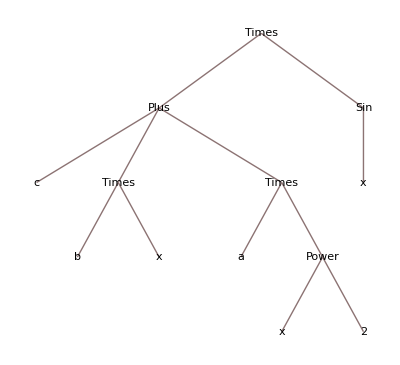

```mathematica
TreeForm[expression]
```

## Дефиниране на променливи и функции от потребителя

```mathematica
a=5; (*";" - потиска резултата от операцията*)
b=10;
```

```mathematica
a+b
```

15

```mathematica
?a
```

Global`a

Важно е да обърнем внимание, че дадена променлива не се дефинира само за текущия файл, а за цялата сесия на програмата, т.е. ако отворим друг файл и в него използваме променливата a, то тя ще има стойност 5. Съществуват механизми за специфициране на обхвата на действие на дадена променлива, с които ще се запознаем по-нататък.

```mathematica
Clear[a] (*Изчиства от паметта записаната в a стойност*)
```

```mathematica
a
```

a

```mathematica
list={1,2,3,4,5};
```

В Mathematica елементите на списъците се достъпват с помощта на двойни квадратни скоби и индексирането започва от 1.

```mathematica
list[[5]]
```

5

```mathematica
list[5]
```

{1,2,3,4,5}[5]

Тъй като вътрешното представяне на всички изрази има списъчна структура, то при опит да достъпим нулев индекс от даден списък, получаваме като резултата Head на този израз:

```mathematica
list[[0]]
```

List

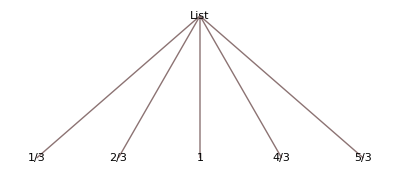

```mathematica
TreeForm[list/3]
```

```mathematica
list2={1,2,abv,{a,rr},55}; (*елементи от произволен тип*)
```

```mathematica
list/3 (*Поелементно пресмятане*)
```

{1/3,2/3,1,4/3,5/3}

### Работа с множества

```mathematica
A={a,a,c,f,f,l};
B={a,c,d,d,f};
Union[A,B]
```

{a,c,d,f,l}

```mathematica
A∪B
```

{a,c,d,f,l}

```mathematica
Intersection[A,B]
```

{a,c,f}

```mathematica
A ∩ B
```

{a,c,f}

```mathematica
{a,c,f}
```

{a,c,f}

```mathematica
Complement[A,B]
```

{l}

### Дефиниране на функции

```mathematica
f[x_]=1/(1+x);
```

Изразът f[x_] в лявата част на дефиницията се нарича образец (pattern) и служи за индикация на класа от изрази, върху които функцията може да действа. В часност, x_ e образец, който означава произволен израз (any expression), т.е. функцията може да приема като параметър произволен обект от системата.

```mathematica
f[5]
```

1/6

```mathematica
f[0.7]
```

0.588235



```mathematica
circle=Graphics[Circle[{0,0},0.1]]
```

```mathematica
f[circle]
```

1/(1+-Graphics-)

Има два начина за дефинриане на функции (и изобщо за присвояване на стойност): lhs=rhs и lhs:=rhs. Основната разлика между двете е кога се пресмята изразът rhs.
 lhs=rhs е незабавно присвояване (immediate assignment), при което изчислението, записано в rhs се прави еднократно, в момента на присвояване.  
 lhs:=rhs е отложено присвояване (delayed assignment), при което оценяването на дясната страна не се извършва в момента на присвояване, а се прави всеки път, коагто lhs е извикана.

```mathematica
randRealSet=RandomReal[]
```

0.0729306

```mathematica
randRealSetDelayed:=RandomReal[]
```

```mathematica
randRealSetDelayed
```

0.913745

```mathematica
randRealSetDelayed
```

0.550765

```mathematica
randRealSet
```

0.0729306

```mathematica
f[x_]=Expand[(x+1)^2];
q[x_]:=Expand[(x+1)^2];
```

```mathematica
?f
```

Global`f

f[x_]=1+2 x+x^2

```mathematica
?q
```

Global`q

q[x_]:=Expand[(x+1)^2]

```mathematica
f[5]
q[5]
```

36

36

```mathematica
Trace[f[5]]
```

{f[5],1+2 5+5^2,{2 5,10},{5^2,25},1+10+25,36}

```mathematica
Trace[q[5]]
```

{q[5],Expand[(5+1)^2],{{5+1,6},6^2,36},Expand[36],36}

Обикновено, когато знаем конкретната стойност, която искаме да присвоим на дадена променлива, използваме “=”. Ако искаме да зададем правило, по което тази стойност да се пресмята, използваме ’’:=’’.
При дефиниране на функции, е по-добре да се използва “:=”, тъй като често пъти, за пресмятанията в тялото на функцията е необходимо да се знае фактическата стойност на някой от параметрите. Ако тя е неизвестна, това би могло да доведе до некоректни резултати:

```mathematica
func[l_]=Length[l]^2;
```

```mathematica
testList={1,2,3};
```

```mathematica
func[testList]
```

0

```mathematica
func2[l_]:=Length[l]^2;
```

```mathematica
func2[testList]
```

9

Въпреки че при дефиниране на функции стандартно трябва да се използва ‘’:= ‘’,  има случаи, в които употребата му може да доведе до нежелани ефекти. Това се дължи на факта, че при отложеното оценяване, първо се замества същинската стойност на параметъра, а след това се извършват пресмятанията:

```mathematica
fff[x_]:=D[Log[Sin[x]]^2,x]
```

```mathematica
fff[1]
```

General::ivar: 1 is not a valid variable.

∂_1 Log[Sin[1]]^2

```mathematica
ff[x_]=D[Log[Sin[x]]^2,x]
```

2 Cot[x] Log[Sin[x]]

```mathematica
ff[1]
```

2 Cot[1] Log[Sin[1]]

```mathematica
---------------------
```

Типът на израза, който дадена функция приема като аргумент, може да бъде указан изрично при дефиницята. За да бъдем съвсем точни - след долната черта се указва Head на съответния израз:

```mathematica
g[x_Real]:=Sqrt[5]*x^2
```

```mathematica
g[0.2]
```

0.0894427

```mathematica
g[2] (*Ако извикаме функцията със същински параметър, който не принадлежи към съответния клас, указан в дефиницията, изчислението няма да бъде изпълнено.*)
```

g[2]

```mathematica
сс
```

### Графики на функции

```mathematica
func[x_]:=Sin[x]^2
func2[x_]:=Cos[3x];
```

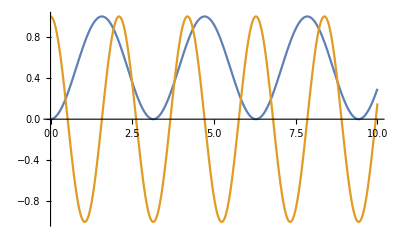

```mathematica
Plot[{func[x],func2[x]},{x,0,10}]
```

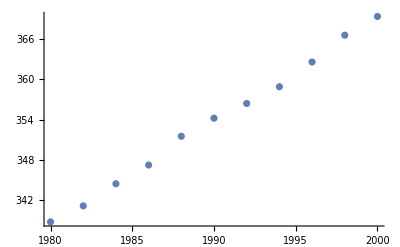

```mathematica
data1={{1980,338.7},{1982,341.1},{1984,344.4},{1986,347.2},{1988,351.5},{1990,354.2},{1992,356.4},{1994,358.9},{1996,362.6},{1998,366.6},{2000,369.4}};
plot1=ListPlot[data1]
```

### Четири вида скоби

Кръгли скоби ( ) - определят приоритета на операциите;
 Квадратни скоби [ ] - заграждат аргументите на функция/команда;
 Фигурни скоби { } - заграждат елементите на списък;
 Двойни квадратни скоби [[ ]] - задават операция по достъпване на елемент от списък. (Двойните квадратни скоби са съкратен запис на функцията Part.)

## Задачи

Зад. 1 Пресметнете:

a) (x+y)^(1/3)+ (x-y)^(1/3) за x=5.1 и y=3.14;
б) √(x/(x+y)+y/(x-y)) при x=1.1 и y=3.14.

Зад. 2 Пресметнете точно, а след това и числено стойността на следните изрази:

a)  [23^3-3(117-48)^2]/(√(7^5-5^7));    б) cos (319π)/12;    в) (83!)/(111!);    г) ln 2981 ;

Зад. 3 Да се пресметне втората прозиводна на функцията f(x) = arctg(√(1+x)-√(1-x)) и да се начертае графиката на тази производна в интервала [0,1].

Зад. 4 Дадени са данни за изменението на нивото на въглеродния диоксид в атмосферата. На база на тези данни да се намери функция,  която описва процесът. За целта да се използва вградената фукнция Fit. Графиката на получената функция да се начертае на една графика с данните.

data1={{1980,338.7},{1982,341.1},{1984,344.4},{1986,347.2},{1988,351.5},{1990,354.2},{1992,356.4},{1994,358.9},{1996,362.6},{1998,366.6},{2000,369.4}};
plot1=ListPlot[data1]
-Graphics-

Зад. 5 Да се напише функция, която намира корените на квадратно уравнение. Функцията да приема като параметри 3 реални числа - коефициентите на квадратния тричлен. 
С помощта на функцията да се намерят корените на уравненението 2 x^2+5x+3=0. Резултатът да се провери графично като се начертаят графиката на квадртаната функция заедно с точките в равнината, отговарящи на получените корени.